449 Hmwk #6
Megan Tabbutt
4/20/18

```mathematica
Import["/Users/megantabbutt/Desktop/Quantum/Defs/448defs.m"]
```

## 4 & 5) By numerical integration of the Schrodinger equation, find the s-wave scattering length and the s-wave cross section as a function of energy for the potential V(r) = -V_0/(1+(r/b)^4) for V_0=9.5 eV and b = 5 a_0. Plot your results from 0 to 10 eV, on a log -log scale. From your zero energy wavefunction, how many bound states are there in this potential? (using prof walker’s s wave scattering notebook)

```mathematica
SE[k_]=p''[s]+k^2 p[s]== 9.5/(1+(s/5)^4)p[s]
```

k^2 p[s]+p''[s]==(9.5 p[s])/(1+s^4/625)

```mathematica
s0=.01;sm=40;p0[s_]=NDSolve[{SE[0],p[0]==0,p'[0]==1},p[s],{s,s0,sm}]⟦1,1,2⟧
```

InterpolatingFunction[…][s]

InterpolatingFunction::dmval: Input value {0.000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

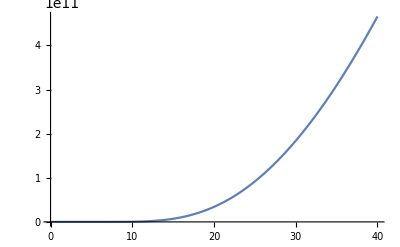

```mathematica
Plot[p0[s],{s,0,40}]
```

```mathematica
sm-p0[sm]/p0'[sm]
```

26.3275

The scattering length is 26.3275

```mathematica
σ0=4π %^2
```

8710.24

The cross section is 8710.24

```mathematica
δ[k_]:=Module[{},pk[s_]=NDSolve[{k^2 p[s]+p''[s]==-34 ⅇ^-s/s p[s],p[s0]==s0,p'[s0]==1},p[s],{s,s0,sm}]⟦1,1,2⟧;
Mod[ArcCot[pk'[sm]/(k pk[sm])]-k sm,π]]
```

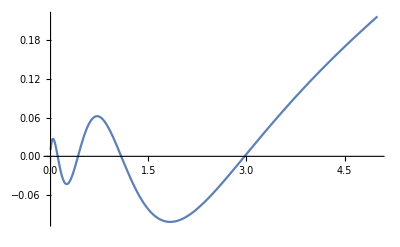

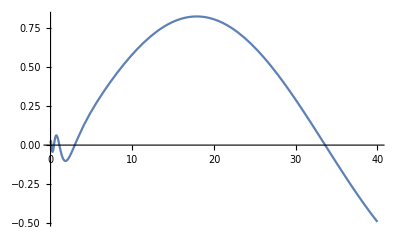

```mathematica
δ[.1];Plot[pk[s],{s,s0,5}]
δ[.1];Plot[pk[s],{s,s0,sm}]
```

There are 5 bound states since there are 5 zero crossings

```mathematica
ks=10^Range[-3,2,.03];
```

```mathematica
σs=Table[{k^2,Sin[δ[k]]^2(4π)/k^2},{k,ks}];
```

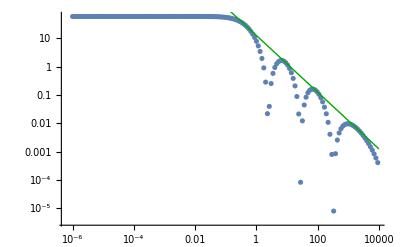

```mathematica
Show[ListLogLogPlot[σs],LogLogPlot[σ0/((1+(σ0 ksq/(4π))^2)^(1/2)),{ksq,.0001,10^4},PlotStyle->{Thick,Darker[Green]}]]
```